# Report project 1

Björn Fredriksson, bfredr@kth.se
Christian Antonio, cantonio@kth.se

## Summary

### Assignment

At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. 

At a fun-fair you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

- Determine the exact (no floating point, please) probability function of the sum.
- Determine the exact probability of winning the Teddy prize. Also give a floating point answer.
- Determine the expected investment to win a Teddy.
- What’s the probability of winning (at least one) Teddy if you play twenty times?

### Result

Den efterfrågade volym som ska transporteras bort kan därmed beräknas enligt

## Method

### Modell för tvärsnittsarea

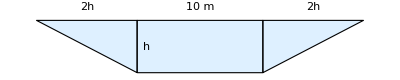

Den givna parallelltrapetsen har arean

a(h)=(10+2h)h

x [m] | h [m] | a [m^2]
0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

Med hjälp av data interpoleras en funktion A(x).

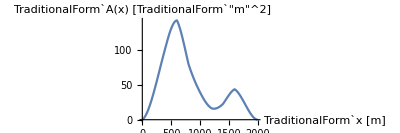

### Modell för volym

Den efterfrågade volym som ska transporteras bort kan beräknas numeriskt ned integralen

V=∫_0^2000 A(x)dx

V≈101 10^3 m^3

Dvs. ca 100 tusen m^3 måste borttransporteras.

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
p1 = ConstantArray[1,4]/4
p2 = ConstantArray[1,6]/6
p3 = ConstantArray[1,8]/8
p4 = ConstantArray[1,12]/12
p5 = ConstantArray[1,20]/20
```

{1/4,1/4,1/4,1/4}

{1/6,1/6,1/6,1/6,1/6,1/6}

{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8}

{1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12}

{1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20}

```mathematica
p23 = ListConvolve[p2,p3,{1,-1},0]
p45 = ListConvolve[p4,p5,{1,-1},0]
```

{1/48,1/24,1/16,1/12,5/48,1/8,1/8,1/8,5/48,1/12,1/16,1/24,1/48}

{1/240,1/120,1/80,1/60,1/48,1/40,7/240,1/30,3/80,1/24,11/240,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,11/240,1/24,3/80,1/30,7/240,1/40,1/48,1/60,1/80,1/120,1/240}

```mathematica
p2345 = ListConvolve[p23,p45,{1,-1},0]
p12345 = ListConvolve[p2345,p1,{1,-1},0]
```

{1/11520,1/2880,1/1152,1/576,7/2304,7/1440,83/11520,29/2880,77/5760,49/2880,241/11520,1/40,67/2304,19/576,211/5760,23/576,493/11520,13/288,541/11520,139/2880,113/2304,71/1440,113/2304,139/2880,541/11520,13/288,493/11520,23/576,211/5760,19/576,67/2304,1/40,241/11520,49/2880,77/5760,29/2880,83/11520,7/1440,7/2304,1/576,1/1152,1/2880,1/11520}

{1/46080,1/9216,1/3072,7/9216,23/15360,121/46080,97/23040,29/4608,409/46080,61/5120,707/46080,293/15360,53/2304,311/11520,95/3072,1597/46080,39/1024,379/9216,1007/23040,211/4608,1091/23040,223/4608,1127/23040,1127/23040,223/4608,1091/23040,211/4608,1007/23040,379/9216,39/1024,1597/46080,95/3072,311/11520,53/2304,293/15360,707/46080,61/5120,409/46080,29/4608,97/23040,121/46080,23/15360,7/9216,1/3072,1/9216,1/46080}